```mathematica
(* The purpose of this document is to plot and compare the spinodals vs both Pe and Per *)
beta=4.0/Pi
phi0=0.90
xi=0.2
```

1.27324

0.9

0.2

```mathematica
(* First we reproduce the monodisperse result (in the space of PeR and Pe) *)
```

```mathematica
(* This formula gives the monodisperse spinodal *)
monoSpinPhiPe[phi_,pe_]:=1-(2*phi)-(3*xi*(phi^2))+(beta*((pe^-1)*(3/2))*(2*phi*((1-(phi/phi0))^-1)+((phi^2)/phi0)*((1-(phi/phi0))^-2)))
```

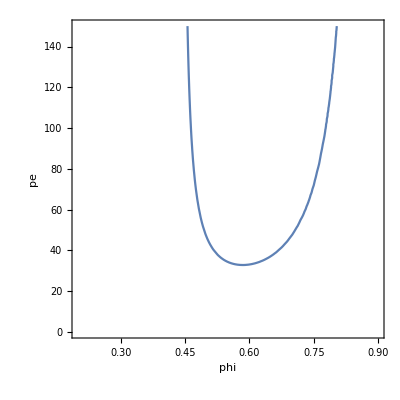

```mathematica
ContourPlot[monoSpinPhiPe[phi,pe]==0, {phi,0.2,0.9},{pe,0,150},AxesLabel->Automatic,PlotLegends->Automatic]
```

```mathematica
(* Great! Looks like this case is working correctly *)
(* Now we try to extend this to the binary case (with just a linear combination of the monodisperse case, a naive method) *)
```

```mathematica
binSpinPhiPe[pea_,peb_,xa_]:=(monoSpinPhiPe[0.6,pea]*xa)+(monoSpinPhiPe[0.6,peb]*(1-xa))
```

```mathematica
ContourPlot3D[binSpinPhiPe[pea,peb,xa]==0,{pea,0,150.0},{peb,0,150.0},{xa,0,1.0},AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
(* Now we'll look at the reorientation peclet number, PeR *)
```

```mathematica
monoSpinPhiPeR[phi_,per_]:=1-(2*phi)-(3*xi*(phi^2))+(beta*(per)*(2*phi*((1-(phi/phi0))^-1)+((phi^2)/phi0)*((1-(phi/phi0))^-2)))
```

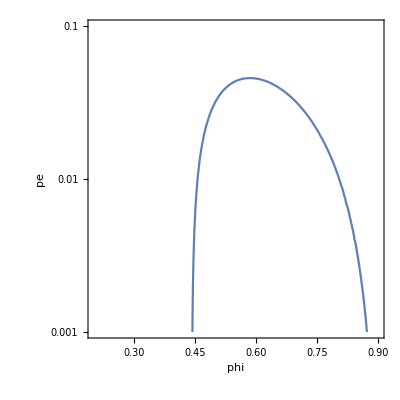

```mathematica
ContourPlot[monoSpinPhiPeR[phi,pe]==0, {phi,0.2,0.9},{pe,10^-3,10^-1},AxesLabel->Automatic,PlotLegends->Automatic,ScalingFunctions->{None,"Log"}]
```

```mathematica
(* Again, this matches up well *)
(* Now let's extend to the binary case (with just a linear combination of the monodisperse case) *)
```

```mathematica
binSpinPhiPeR[pera_,perb_,xa_]:=(monoSpinPhiPeR[0.6,pera]*xa)+(monoSpinPhiPeR[0.6,perb]*(1-xa))
```

```mathematica
ContourPlot3D[binSpinPhiPeR[pera,perb,xa]==50000,{pera,0.01,10000},{perb,0.01,10000},{xa,-0.1,1.1},AxesLabel->Automatic,PlotLegends->Automatic]
```

-Graphics3D-

```mathematica
(* A linear combination does not match up well with the results we have for binary active/active mixtures *)
```

```mathematica
(* Now we'll take a look at the correct derived form *)
```

```mathematica
derivedBinSpinPE[phi_,pea_,peb_,xa_]:=((((pea^-1)*(3/2)))^-2)*
(1-(2*phi)-(3*xi*(phi^2))+(beta*((pea^-1)*(3/2)))*
(
(2*phi)*((1-(phi/phi0))^-1)+(((phi^2)/phi0)*((1-(phi/phi0))^-2))
))*xa+
((((peb^-1)*(3/2)))^-2)*
(1-(2*phi)-(3*xi*(phi^2))+(beta*((peb^-1)*(3/2)))*
(
(2*phi)*((1-(phi/phi0))^-1)+(((phi^2)/phi0)*((1-(phi/phi0))^-2))
))*(1-xa)
```

```mathematica
ContourPlot3D[derivedBinSpinPE[0.6,pea,peb,xa]==0,{pea,0,150},{peb,0,150},{xa,0,1},AxesLabel->Automatic,PlotLegends->Automatic]
ContourPlot3D[derivedBinSpinPE[0.6,pea,peb,xa]==-150,{pea,0,150},{peb,0,150},{xa,0,1},AxesLabel->Automatic,PlotLegends->Automatic]
```

-Graphics3D-

-Graphics3D-

```mathematica
(* These look better, but they still have some unphysical features. (If you increase activity this should only ever increase the propensity for phase separation) *)
```

```mathematica
(* And in the the Brady form PeR *)
```

```mathematica
derivedBinSpinPER[phi_,pera_,perb_,xa_]:=((pera)^-2)*
(1-(2*phi)-(3*xi*(phi^2))+(beta*pera)*
(
(2*phi)*((1-(phi/phi0))^-1)+(((phi^2)/phi0)*((1-(phi/phi0))^-2))
))*xa+
((perb)^-2)*
(1-(2*phi)-(3*xi*(phi^2))+(beta*perb)*
(
(2*phi)*((1-(phi/phi0))^-1)+(((phi^2)/phi0)*((1-(phi/phi0))^-2))
))*(1-xa)
```

```mathematica
ContourPlot3D[derivedBinSpinPER[0.6,pera,perb,xa]==0,{pera,10^-3,10^-1},{perb,10^-3,10^-1},{xa,0,1},AxesLabel->Automatic,PlotLegends->Automatic]
```

-Graphics3D-

```mathematica
(* This method predicts reentrance in the unstable regime. This doesn't look like the right fit either *)
```